```mathematica
h=1/2f1 √(Jx Jy)Cos[ϕx-ϕy+2(δ s)/R]+(p Jx^2+r Jy^2)+f2 Jx Jy (2+Cos[2ϕx-2ϕy+4(δ s)/R]);
```

```mathematica
Simplify[(D[h+δ/R(Jx-Jy),Jx]-D[h+δ/R(Jx-Jy),Jy]-(D[h,Jx]-D[h,Jy]+2δ/R))/.{Jx->(II+J)/2,Jy->(II-J)/2,ϕx->ϕy-(2 δ s)/R+Φ}]
```

0

```mathematica
Simplify[((D[h,Jx]-D[h,Jy]+2δ/R)/.{Jx->(II+J)/2,Jy->(II-J)/2,ϕx->ϕy-(2 δ s)/R+Φ})-Simplify[D[∫((2D[h,ϕx])/.{Jx->(II+J)/2,Jy->(II-J)/2,ϕx->ϕy-(2 δ s)/R+Φ})ⅆΦ,J]]]
```

-f2 J+J p+II (p-r)+J r+(2 δ)/R

```mathematica
hnew=Simplify[∫((2D[h,ϕx])/.{Jx->(II+J)/2,Jy->(II-J)/2,ϕx->ϕy-(2 δ s)/R+Φ})ⅆΦ+∫(-f2 J+J p+II (p-r)+J r+(2 δ)/R)ⅆJ];
```

```mathematica
Simplify[D[hnew,Φ]-2D[h,ϕx]/.{Jx->(II+J)/2,Jy->(II-J)/2,ϕx->ϕy-(2 δ s)/R+Φ}]
```

0

```mathematica
Simplify[D[hnew,J]-((D[h,Jx]-D[h,Jy]+2δ/R)/.{Jx->(II+J)/2,Jy->(II-J)/2,ϕx->ϕy-(2 δ s)/R+Φ})]
```

0

```mathematica
Simplify[((D[h,Jx]+D[h,Jy])/.{Jx->(II+J)/2,Jy->(II-J)/2,ϕx->ϕy-(2 δ s)/R+Φ})-D[hnew,II]]
```

II (f2+p+r)

```mathematica
hnew1=Simplify[hnew+1/2 II^2 (f2+p+r)+II ν0+J δ/R]
```

1/2 (-f2 J^2+J^2 p+2 II J (p-r)+J^2 r+II^2 (f2+p+r)+(6 J δ)/R+2 II ν0+f1 √(II^2-J^2) Cos[Φ]+2 f2 (II^2-J^2) Cos[Φ]^2)

```mathematica
Simplify[Cos[α]Cos[Φ]-Sin[α]Sin[Φ]]
```

Cos[α+Φ]

```mathematica
Simplify[((D[h,Jx]+D[h,Jy])/.{Jx->(II+J)/2,Jy->(II-J)/2,ϕx->ϕy-(2 δ s)/R+Φ})-D[hnew1,II]]
```

-ν0

```mathematica
hnew11=hnew1/.{J->a J,II->a II};
```

```mathematica
Manipulate[ContourPlot[hnew11/.{II->1,δ->-0.001,f2->a1,p->0,r->0,f1->10 0.0002,R->1/π,a->0.0002,ν0->0.17},{Φ,-π,π},{J,-1,1}],{a1,0,100}]
```

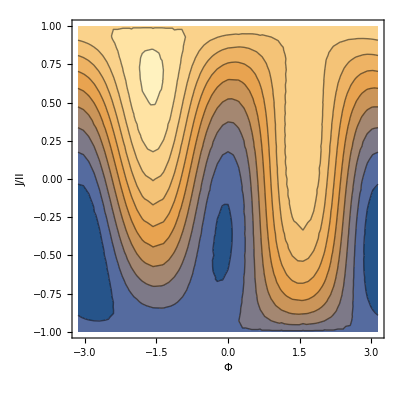

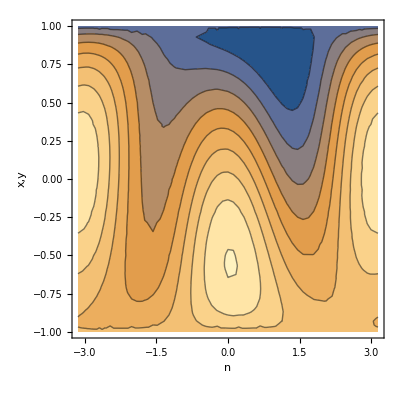

```mathematica
aplot=ContourPlot[hnew11/.{II->1,δ->0.001,f2->-60,p->15,q->20,r->40,k11->-25,k12->35,R->1/π,a->.0002,α->5},{Φ,-π,π},{J,-1,1},AxesLabel->{"Φ","J/II"},LabelStyle->Directive[Black, 14]]
bplot=ContourPlot[hnew11/.{II->1,δ->-0.001,f2->40,p->10,q->20,r->-30,k11->55,k12->-35,R->1/π,a->.0002,α->2.7},{Φ,-π,π},{J,-1,1},AxesLabel->{"n","x,y"},LabelStyle->Directive[Black, 14]]
```

```mathematica
ΦStr=100000(D[hnew11,J]/.{J->J[t],Φ->Φ[t]})/.{II->1,δ->0.001,f2->0,k11->-50,k12->50,p->0,r->0,q->-0,R->1/π,a->.0002,α->0};
JStr=-100000(D[hnew11,Φ]/.{J->J[t],Φ->Φ[t]})/.{II->1,δ->0.001,f2->0,k11->-50,k12->50,p->0,r->0,q->-0,R->1/π,a->.0002,α->0};

(*"nach.uslov."*)

plot2=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot2],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot3=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.89,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot3],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot4=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot4],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot5=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.7,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot5],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot6=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot6],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot7=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.5,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot7],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot8=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.4,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot8],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot9=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot9],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot10=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.2,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot10],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot11=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.1,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot11],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot12=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==0,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot12],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot13=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.1,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot13],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot20=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.2,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P20=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot20],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot14=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot14],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot15=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.4,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P15=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot15],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot16=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.5,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P16=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot16],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot17=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P17=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot17],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->Thickness[.001]];
plot18=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.7,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P18=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot18],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True,PlotStyle->PointSize[0.001]];
plot19=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P19=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot19],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini1=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.89,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.59,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.29,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->0.01,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.31,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.61,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.91,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.99,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.89,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.79,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.69,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.59,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.49,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];
pini14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.39,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z},PlotStyle->Thickness[.001]];

Show[{P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20,pini1,pini2,pini3,pini4,pini5,pini6,pini7},PlotRange->Full,AxesLabel->{x,y,z},LabelStyle->Directive[Black, 30]]
```

-Graphics3D-

```mathematica
ΦStr=1000000(D[hnew11,J]/.{J->J[t],Φ->Φ[t]})/.{II->1,δ->0.001,f2->20,p->10,q->-15,r->40,k11->-20,k12->10,R->1/π,a->.0002,α->0};
JStr=-1000000(D[hnew11,Φ]/.{J->J[t],Φ->Φ[t]})/.{II->1,δ->0.001,f2->20,p->10,q->-15,r->40,k11->-20,k12->10,R->1/π,a->.0002,α->0};

(*"nach.uslov."*)

plot2=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.95,Φ[0]==π/2},{J[t],Φ[t]},{t,0,180}];
P2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot2],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot3=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.9,Φ[0]==π/2},{J[t],Φ[t]},{t,0,180}];
P3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot3],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot4=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.8,Φ[0]==π/2},{J[t],Φ[t]},{t,0,180}];
P4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot4],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot5=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot5],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot6=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot6],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot7=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==0,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot7],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot8=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot8],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot9=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot9],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot10=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot10],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot11=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.9,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot11],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot12=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.95,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot12],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot13=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot13],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot20=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P20=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot20],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot14=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.7,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot14],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot15=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.9,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P15=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot15],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot16=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.4,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P16=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot16],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot17=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.49,Φ[0]==π/2},{J[t],Φ[t]},{t,0,180}];
P17=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot17],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot18=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.39,Φ[0]==π/2},{J[t],Φ[t]},{t,0,180}];
P18=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot18],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot19=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.1,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P19=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot19],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
pini1=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.99,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.89,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.79,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.69,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.59,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.49,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.39,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.99,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.89,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.79,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.69,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.59,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.49,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.39,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];

Show[{P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20,pini1,pini2,pini3,pini4,pini5,pini6,pini7,pini8,pini9,pini10,pini11,pini12,pini13,pini14},PlotRange->Full,AxesLabel->{x,y,z},LabelStyle->Directive[Black, 30]]
```

-Graphics3D-

```mathematica
ΦStr=100000(D[hnew11,J]/.{J->J[t],Φ->Φ[t]})/.{II->1,δ->0.001,f2->50,k11->-50,k12->50,p->0,r->0,q->-0,R->1/π,a->.0002,α->0};
JStr=-100000(D[hnew11,Φ]/.{J->J[t],Φ->Φ[t]})/.{II->1,δ->0.001,f2->50,k11->-50,k12->50,p->0,r->0,q->-0,R->1/π,a->.0002,α->0};

(*"nach.uslov."*)

plot2=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot2],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot3=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.95,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot3],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot4=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot4],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot5=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.7,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot5],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot6=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot6],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot7=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.5,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot7],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot8=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.4,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot8],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot9=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot9],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot10=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.2,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot10],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot11=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.1,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot11],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot12=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==0.6,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot12],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot13=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.1,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot13],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot20=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.2,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P20=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot20],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot14=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot14],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot15=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.4,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P15=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot15],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot16=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.5,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P16=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot16],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot17=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.5,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P17=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot17],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot18=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.7,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P18=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot18],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot19=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.4,Φ[0]==0},{J[t],Φ[t]},{t,0,180}];
P19=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot19],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
pini1=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.9,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.6,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.3,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.3,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.6,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.9,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->0.99,Φ[t]->0}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->0.89,Φ[t]->0}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->0.79,Φ[t]->0}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.69,Φ[t]->0}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->0.59,Φ[t]->0}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.49,Φ[t]->0}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.39,Φ[t]->0}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];

Show[{P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20,pini1,pini2,pini3,pini4,pini5,pini6,pini7,pini8,pini9,pini10,pini11,pini12,pini13,pini14},PlotRange->Full,AxesLabel->{x,y,z},LabelStyle->Directive[Black, 30]]
```

-Graphics3D-

```mathematica
ΦStr=100000(D[hnew11,J]/.{J->J[t],Φ->Φ[t]})/.{II->1,δ->0.001,f2->20,p->30,q->-60,r->-50,k11->-20,k12->10,R->1/π,a->.0002,α->0};
JStr=-100000(D[hnew11,Φ]/.{J->J[t],Φ->Φ[t]})/.{II->1,δ->0.001,f2->20,p->30,q->-60,r->-50,k11->-20,k12->10,R->1/π,a->.0002,α->0};

(*"nach.uslov."*)

plot2=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.99,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot2],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot3=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.95,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot3],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot4=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot4],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot5=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.7,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot5],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot6=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot6],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot7=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.5,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot7],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot8=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.4,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot8],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot9=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot9],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot10=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.2,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot10],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot11=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==-.1,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot11],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot12=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==0,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot12],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot13=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.1,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot13],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot20=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.2,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P20=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot20],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot14=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.3,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot14],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot15=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.4,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P15=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot15],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot16=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.5,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P16=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot16],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot17=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.6,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P17=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot17],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot18=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.7,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P18=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot18],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,Axes->True];
plot19=NDSolve[{J'[t]==JStr,Φ'[t]==ΦStr,J[0]==.8,Φ[0]==π},{J[t],Φ[t]},{t,0,180}];
P19=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.plot19],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black,AxesLabel->{x,y,z}];
pini1=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.9,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini2=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.6,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini3=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.3,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini4=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini5=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.3,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini6=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.6,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini7=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->.9,Φ[t]->π}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Red,Thickness[.03]},AxesLabel->{x,y,z}];
pini8=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.99,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini9=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.89,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini10=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.79,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini11=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.69,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini12=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-0.59,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini13=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.49,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];
pini14=ParametricPlot3D[Evaluate[{Cos[Φ[t]] √(1-J[t]^2),Sin[Φ[t]] √(1-J[t]^2),J[t]}/.{J[t]->-.39,Φ[t]->π/2}],{t,0,180},PlotRange->{{-1,1},{-1,1}},PlotStyle->{Blue,Thickness[.03]},AxesLabel->{x,y,z}];

Show[{P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20,pini1,pini2,pini3,pini4,pini5,pini6,pini7},PlotRange->Full,AxesLabel->{x,y,z}]
```

-Graphics3D-